# 沃罗内网格

```mathematica
a=Table[2i,{i,1,10}];
```

### 建立纵坐标组

```mathematica
b=a-1
```

{1,3,5,7,9,11,13,15,17,19}

```mathematica
c=Riffle[Table[a,10],{b}]//Flatten
```

{2,4,6,8,10,12,14,16,18,20,1,3,5,7,9,11,13,15,17,19,2,4,6,8,10,12,14,16,18,20,1,3,5,7,9,11,13,15,17,19,2,4,6,8,10,12,14,16,18,20,1,3,5,7,9,11,13,15,17,19,2,4,6,8,10,12,14,16,18,20,1,3,5,7,9,11,13,15,17,19,2,4,6,8,10,12,14,16,18,20,1,3,5,7,9,11,13,15,17,19,2,4,6,8,10,12,14,16,18,20,1,3,5,7,9,11,13,15,17,19,2,4,6,8,10,12,14,16,18,20,1,3,5,7,9,11,13,15,17,19,2,4,6,8,10,12,14,16,18,20,1,3,5,7,9,11,13,15,17,19,2,4,6,8,10,12,14,16,18,20,1,3,5,7,9,11,13,15,17,19,2,4,6,8,10,12,14,16,18,20}

### 建立横坐标组

```mathematica
d=Table[Sqrt[3]*i,{i,1,19},{j,1,10}]//Flatten;
```

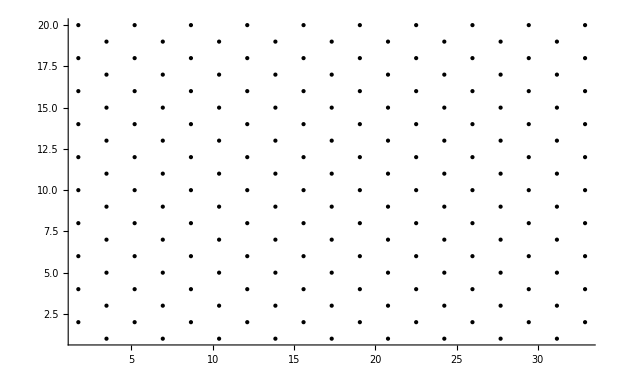

```mathematica
Partition[Riffle[d,c],2]//Point//Graphics[#,Axes->True]&
```

k作为畸变率

```mathematica
k=3;
```

```mathematica
rho=RandomReal[{0,1},Length[c]]*k;
```

```mathematica
theta=RandomReal[{0,1},Length[c]]*2Pi;
```

### 计算横坐标畸变

```mathematica
dd=d+rho*Cos[theta];
```

### 纵坐标畸变

```mathematica
cc=c+rho*Sin[theta];
```

### 畸变后的点阵

```mathematica
l=Partition[Riffle[dd,cc],2];
```

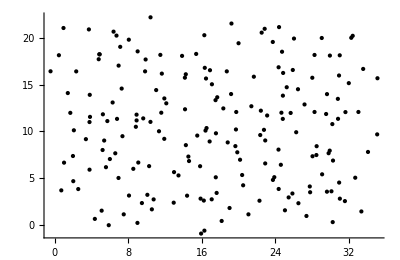

```mathematica
l//Point//Graphics[#,Axes->True]&
```

### 沃罗内网格

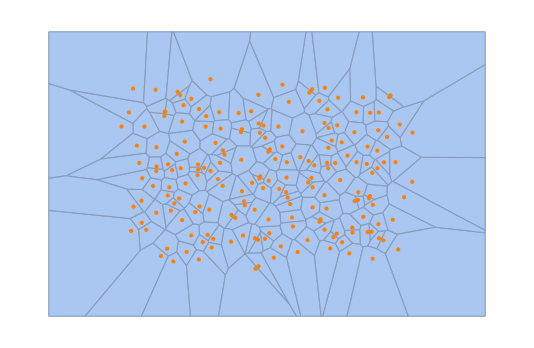

```mathematica
Show[VoronoiMesh[Partition[Riffle[dd,cc],2]],Graphics[{Orange,Point[l]}]]
```

## 一条龙服务：

### 生成点阵的函数：

行数为x，列数为2y-1的点阵的生成方法：

```mathematica
GeneratePoints[x_,y_,q_]:=Module[{a,b,c,d},
a=Table[2i*q,{i,1,x}];
b=a-1*q;
c=Riffle[Table[a,y],{b}]//Flatten;
d=Table[Sqrt[3]*i*q,{i,1,2y-1},{j,1,x}]//Flatten;
Return[Partition[Riffle[d,c],2]]
]
```

举个例子，一列有3个点，一共有5列的点阵：

```mathematica
GeneratePoints[3,3,0.1]
```

{{0.173205,0.2},{0.173205,0.4},{0.173205,0.6},{0.34641,0.1},{0.34641,0.3},{0.34641,0.5},{0.519615,0.2},{0.519615,0.4},{0.519615,0.6},{0.69282,0.1},{0.69282,0.3},{0.69282,0.5},{0.866025,0.2},{0.866025,0.4},{0.866025,0.6}}

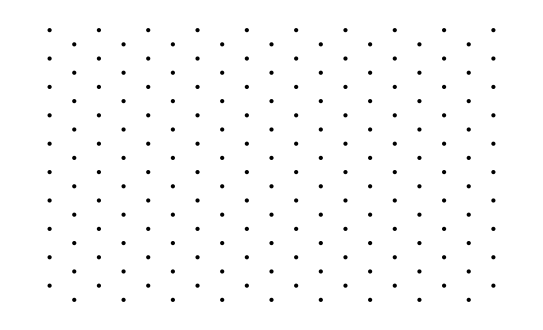

```mathematica
GeneratePoints[10,10,0.1]//Point//Graphics[#,Axes->Automatic]&
```

### 畸变

行数为x，列数为2y - 1 的点阵的畸变率为k的畸变方法：

```mathematica
Distortion[x_,y_,k_]:=Module[{a,b,c,d,rho,theta,dd,cc,l},
a=Table[2i,{i,1,x}];
b=a-1;
c=Riffle[Table[a,y],{b}]//Flatten;
d=Table[Sqrt[3]*i,{i,1,2y-1},{j,1,x}]//Flatten;
rho=RandomReal[{0,1},Length[c]]*k;
theta=RandomReal[{0,1},Length[c]]*2Pi;
dd=d+rho*Cos[theta];
cc=c+rho*Sin[theta];
l=Partition[Riffle[dd,cc],2];
Return[l]
]
```

示例：

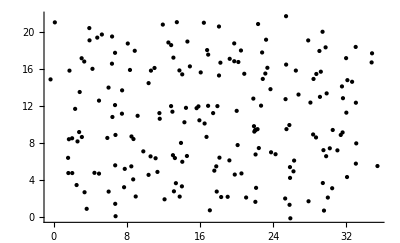

```mathematica
Distortion[10,10,3]//Point//Graphics[#,Axes->True]&
```

### 沃罗内

沃罗内网格用内置函数就行，不需要编了……

```mathematica
RandomReal[{0,1},10000,WorkingPrecision->10]//Total
```

5017.223541

### 指定范围和颗粒的解决方案

```mathematica
GeneratePoints[x_,y_,q_]:=Module[{a,b,c,d},a=Table[2 i*q,{i,1,x}];
b=a-1*q;
c=Riffle[Table[a,y],{b}]//Flatten;
d=Table[Sqrt[3]*i*q,{i,1,2 y-1},{j,1,x}]//Flatten;
Return[Partition[Riffle[d,c],2]]]
```

## 限定区域畸变

## 假定你已经得到一个经过缩放的点阵

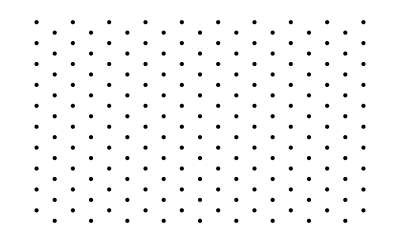

```mathematica
GeneratePoints[10,10,1]//Point//Graphics[#,Axes->Automatic]&
```

### 定义一个畸变函数

函数名称为Distote，作用是对一个点x进行畸变，畸变率为k

```mathematica
Distote[x_,k_]:=Module[{rho,theta},
rho=RandomReal[]*k;
theta=RandomReal[]*2Pi;
Return[{x[[1]]+rho*Cos[theta],x[[2]]+Sin[theta]}]
]
```

示例：

```mathematica
Distote[{10,20},500]
```

{-243.835,20.8283}

定义一个函数，能够对点阵x中横坐标属于y，纵坐标属于z的点进行畸变，畸变率为k。

```mathematica
DistoteField[x_,y_,z_,k_]:=Replace[x,{m_/;Between[m[[1]],y]==True&&Between[m[[2]],z]==True:>Distote[m,k]},{1}]
```

### 注意：！GeneradePoint指令中的放大率以及DistoteField以及畸变范围一定要用机器数，如1要输入成1.0（如果不这样的话程序会在某些情况下失效，原因我还没找到）

```mathematica
p=GeneratePoints[10,10,1];
```

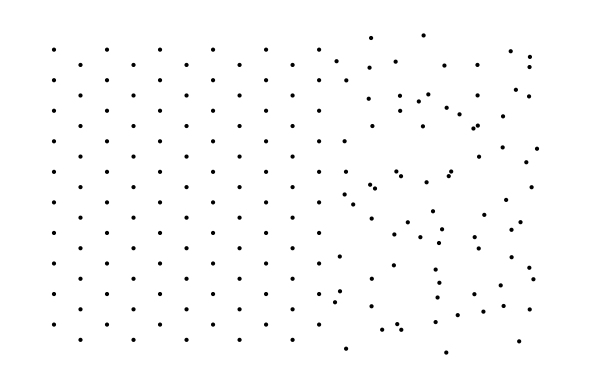

```mathematica
DistoteField[p,{20,50},{0,20},1]//Point//Graphics[#,Axes->Automatic]&
```

### 以下定义函数，做到划分5个区域，分别设定畸变率

我们挑选最中间的一块区域，将它的左上顶点设为(x1,y1)，右下顶点作为(x2,y2)。

```mathematica
DistoteFieldUniversal[p_,{x1_,x2_,y1_,y2_},{k1_,k2_,k3_,k4_,k5_}]:=Replace[p,
(*定义中间块*)
{m_/;Simplify[(x1<=m[[1]]<=x2)]==True&&Simplify[(y1<=m[[2]]<=y2)]==True:>Distote[m,k2],
(*定义左块*)
m_/;Simplify[(m[[1]]<=x1)]==True:>Distote[m,k1],
(*定义右块*)
m_/;Simplify[(x2<=m[[1]])]==True:>Distote[m,k3],
(*定义上块*)
m_/;Simplify[(x1<=m[[1]]<=x2)]==True&&Simplify[m[[2]]>=y2]==True:>Distote[m,k4],
(*定义下块*)
m_/;Simplify[(x1<=m[[1]]<=x2)]==True&&Simplify[m[[2]]<=y1]==True:>Distote[m,k5]}

,{1}]
```

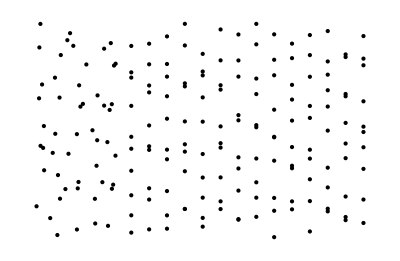

```mathematica
DistoteFieldUniversal[p,{10.,20.,5.,15.},{1.0,0.0,0.0,0.0,0.0}]//Point//Graphics[#,Axes->Automatic]&
```

### 下面这里不用管，是我自己的疑问，跟这个任务无关的，我觉得这个问题有意义所以才不删。

why?  我的预期是替换为1的那列结果应该是{1,1,1,1,1,1,1}

```mathematica
{1,2,3}/.{x_/;(Print[x];Head[x]==Integer)->1}
```

{1,2,3}

List

1

2

3

{1,1,1}